# Slepton-side virtual contribution

```mathematica
description="Slepton-side virtual contribution";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts","FeynHelpers"};
<<FeynCalc`
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples.The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

```mathematica
$KeepLogDivergentScalelessIntegrals = True;
```

```mathematica
$ToolsRoot=ParentDirectory[NotebookDirectory[]];
AppendTo[$Path,FileNameJoin[{$ToolsRoot,"Include"}]];
<<Tools`
<<PrettyNotation`
```

## Find amplitudes

### Draw diagrams

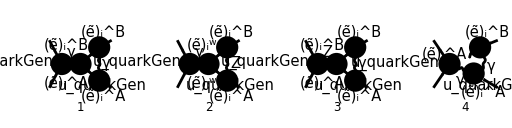

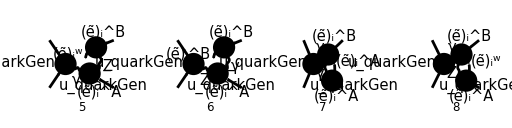

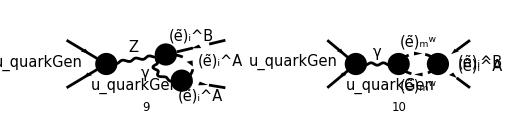

```mathematica
diags[0]=InsertFields[
CreateTopologies[1,2->2,ExcludeTopologies->{Tadpoles,SelfEnergies,Boxes}],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{S[1],S[2],S[3],S[4],S[5],S[6],V[3],F[11],F[12],S[13],S[14],S[11]},
LastSelections->{V[1],S[12]}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

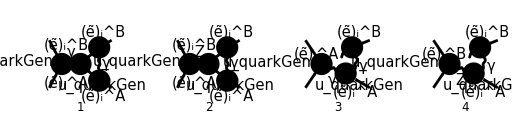

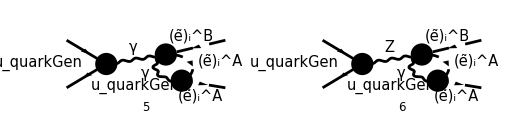

```mathematica
diags[1]=DiagramExtract[diags[0],{1,3,4,6,7,9}];
Paint[
diags[1],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

### Find Amplitudes

```mathematica
Mlist[0]=FCFAConvert[
CreateFeynAmp[diags[1]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k2},
LoopMomenta->{kloop},
ChangeDimension->D,
UndoChiralSplittings->True,
Contract->False,
LorentzIndexNames->{μ,ν,ρ,σ},
DropSumOver->True,
SMP->True,
List->True
]/.{MQU[quarkGen]->0}
```

{((φ(-p_2)).(-2/3 ⅈ γ^μ e δ_Col1Col2).(φ(p_1)) IndexDelta(A,B) g^μν (-k_1+k_2-2 kloop)^ν g^ρσ (-2 k_1-kloop)^ρ (kloop-2 k_2)^σ e^3)/(16 π^4 kloop^2.((k_1+kloop)^2-m_l_iB^2).((kloop-k_2)^2-m_l_iA^2) (k_1+k_2)^2),-(((φ(-p_2)).((2 ⅈ γ^μ.(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ γ^μ.(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) g^μν (-k_1+k_2-2 kloop)^ν g^ρσ (-2 k_1-kloop)^ρ (kloop-2 k_2)^σ e^3 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(32 π^4 kloop^2.((k_1+kloop)^2-m_l_iB^2).((kloop-k_2)^2-m_l_iA^2) ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))),((φ(-p_2)).(-2/3 ⅈ γ^μ e δ_Col1Col2).(φ(p_1)) IndexDelta(A,B) g^μν g^νσ g^ρσ (kloop-k_1)^ρ e^3)/(8 π^4 (kloop^2-m_l_iA^2).(k_1+kloop)^2 (k_1+k_2)^2),-(((φ(-p_2)).((2 ⅈ γ^μ.(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ γ^μ.(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) g^μν g^νσ g^ρσ (kloop-k_1)^ρ e^3 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(16 π^4 (kloop^2-m_l_iB^2).(k_1+kloop)^2 ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))),-((φ(-p_2)).(-2/3 ⅈ γ^μ e δ_Col1Col2).(φ(p_1)) IndexDelta(A,B) g^μν g^νσ g^ρσ (kloop-k_2)^ρ e^3)/(8 π^4 (kloop^2-m_l_iA^2).(k_2+kloop)^2 (k_1+k_2)^2),((φ(-p_2)).((2 ⅈ γ^μ.(γ̄)^6 e (sin(θ_W)) δ_Col1Col2)/(3 (cos(θ_W)))+(ⅈ γ^μ.(γ̄)^7 e (4 (sin(θ_W))^2-3) δ_Col1Col2)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(p_1)) g^μν g^νσ g^ρσ (kloop-k_2)^ρ e^3 (2 Conjugate[(USf(2,i)(B,2))] USf(2,i)(A,2) (sin(θ_W))^2+Conjugate[(USf(2,i)(B,1))] (2 (sin(θ_W))^2-1) USf(2,i)(A,1)))/(16 π^4 (kloop^2-m_l_iA^2).(k_2+kloop)^2 ((k_1+k_2)^2-m_Z^2) (cos(θ_W)) (sin(θ_W)))}

```mathematica
M1γ[0]=Mlist[0][[1]]3/2SMP["e_Q"]
M1γ[1]=M1γ[0]//TID[#,kloop,ToPaVe->True]&//Simplify
```

(3 e^3 e_Q g^μν g^ρσ (-k_1+k_2-2 kloop)^ν (-2 k_1-kloop)^ρ (kloop-2 k_2)^σ IndexDelta(A,B) (φ(-p_2)).(-2/3 ⅈ e γ^μ δ_Col1Col2).(φ(p_1)))/(32 π^4 (k_1+k_2)^2 kloop^2.((k_1+kloop)^2-m_l_iB^2).((kloop-k_2)^2-m_l_iA^2))

1/(16 π^2 (k_1+k_2)^2)IndexDelta(A,B) (A_0(m_l_iB^2) (-((φ(-p_2)).(γ·k_1).(φ(p_1)))/k_1^2-((φ(-p_2)).(-(γ·(k_1+k_2))).(φ(p_1)))/(k_1^2+2 (k_1·k_2)+k_2^2))+A_0(m_l_iA^2) (((φ(-p_2)).(γ·k_2).(φ(p_1)))/k_2^2+((φ(-p_2)).(-(γ·(k_1+k_2))).(φ(p_1)))/(k_1^2+2 (k_1·k_2)+k_2^2))-(B_0(k_1^2+2 (k_1·k_2)+k_2^2,m_l_iA^2,m_l_iB^2) (2 (φ(-p_2)).(γ·k_1).(φ(p_1)) (k_1·k_2)^3+2 (φ(-p_2)).(-(γ·(k_1+k_2))).(φ(p_1)) (k_1·k_2)^3-(φ(-p_2)).(-(γ·(k_1+k_2))).(φ(p_1)) m_l_iA^2 (k_1·k_2)^2+(φ(-p_2)).(-(γ·(k_1+k_2))).(φ(p_1)) m_l_iB^2 (k_1·k_2)^2+(φ(-p_2)).(γ·k_1).(φ(p_1)) k_1^2 (k_1·k_2)^2+(φ(-p_2)).(-(γ·(k_1+k_2))).(φ(p_1)) k_1^2 (k_1·k_2)^2-7 (φ(-p_2)).(γ·k_1).(φ(p_1)) k_2^2 (k_1·k_2)^2+(φ(-p_2)).(-(γ·(k_1+k_2))).(φ(p_1)) k_2^2 (k_1·k_2)^2-6 (φ(-p_2)).(γ·k_1).(φ(p_1)) k_2^4 (k_1·k_2)+2 (φ(-p_2)).(γ·k_1).(φ(p_1)) m_l_iA^2 k_2^2 (k_1·k_2)+2 (φ(-p_2)).(γ·k_1).(φ(p_1)) m_l_iB^2 k_2^2 (k_1·k_2)-8 (φ(-p_2)).(γ·k_1).(φ(p_1)) k_1^2 k_2^2 (k_1·k_2)-2 (φ(-p_2)).(-(γ·(k_1+k_2))).(φ(p_1)) k_1^2 k_2^2 (k_1·k_2)+(φ(-p_2)).(-(γ·(k_1-k_2))).(φ(p_1)) (k_1^2+2 (k_1·k_2)+k_2^2) (-m_l_iA^2-m_l_iB^2+k_1^2+4 (k_1·k_2)+k_2^2) (k_1·k_2)-(φ(-p_2)).(γ·k_1).(φ(p_1)) k_2^6+(φ(-p_2)).(γ·k_1).(φ(p_1)) m_l_iA^2 k_2^4+(φ(-p_2)).(γ·k_1).(φ(p_1)) m_l_iB^2 k_2^4-3 (φ(-p_2)).(γ·k_1).(φ(p_1)) k_1^2 k_2^4-(φ(-p_2)).(-(γ·(k_1+k_2))).(φ(p_1)) k_1^2 k_2^4-2 (φ(-p_2)).(γ·k_1).(φ(p_1)) k_1^4 k_2^2-(φ(-p_2)).(-(γ·(k_1+k_2))).(φ(p_1)) k_1^4 k_2^2+(φ(-p_2)).(γ·k_1).(φ(p_1)) m_l_iA^2 k_1^2 k_2^2+(φ(-p_2)).(-(γ·(k_1+k_2))).(φ(p_1)) m_l_iA^2 k_1^2 k_2^2+(φ(-p_2)).(γ·k_1).(φ(p_1)) m_l_iB^2 k_1^2 k_2^2-(φ(-p_2)).(-(γ·(k_1+k_2))).(φ(p_1)) m_l_iB^2 k_1^2 k_2^2-(φ(-p_2)).(γ·k_2).(φ(p_1)) (k_1^2 m_l_iA^2-k_1^4-(k_1·k_2)^2+m_l_iB^2 k_1^2-4 k_1^2 (k_1·k_2)) (k_1^2+2 (k_1·k_2)+k_2^2)))/((k_1^2+2 (k_1·k_2)+k_2^2) (k_1^2 k_2^2-(k_1·k_2)^2))-1/(k_1^2 k_2^2-(k_1·k_2)^2)C_0(k_1^2,k_2^2,k_1^2+2 (k_1·k_2)+k_2^2,m_l_iB^2,0,m_l_iA^2) (m_l_iA^2+m_l_iB^2-k_1^2-4 (k_1·k_2)-k_2^2) ((φ(-p_2)).(γ·k_2).(φ(p_1)) (k_1^2 m_l_iA^2+(m_l_iB^2-k_1^2-k_1·k_2) (k_1·k_2))+(φ(-p_2)).(γ·k_1).(φ(p_1)) (-(k_1·k_2) m_l_iA^2+(k_1·k_2)^2-m_l_iB^2 k_2^2+(k_1·k_2) k_2^2))+1/(k_2^2 (k_1^2 k_2^2-(k_1·k_2)^2))B_0(k_2^2,0,m_l_iA^2) ((φ(-p_2)).(γ·k_2).(φ(p_1)) (((k_1·k_2)^2-k_2^2 (k_1·k_2)-k_1^2 k_2^2) m_l_iA^2+(k_1·k_2) k_2^2 (-m_l_iB^2+k_1^2+4 (k_1·k_2)+k_2^2))-(φ(-p_2)).(γ·k_1).(φ(p_1)) k_2^2 ((k_1·k_2)^2+4 k_2^2 (k_1·k_2)+k_2^2 (-m_l_iA^2-m_l_iB^2+k_2^2)))+1/(k_1^2 (k_1^2 k_2^2-(k_1·k_2)^2))B_0(k_1^2,0,m_l_iB^2) ((φ(-p_2)).(γ·k_2).(φ(p_1)) k_1^2 (-k_1^2 m_l_iA^2+k_1^4+(k_1·k_2)^2-m_l_iB^2 k_1^2+4 k_1^2 (k_1·k_2))+(φ(-p_2)).(γ·k_1).(φ(p_1)) (k_1^2 (k_1·k_2) m_l_iA^2-k_1^2 (k_1·k_2) (k_1^2+4 (k_1·k_2)+k_2^2)+m_l_iB^2 (k_1^2 (k_1·k_2+k_2^2)-(k_1·k_2)^2)))) e^4 e_Q δ_Col1Col2

```mathematica
M1Z[0]=Mlist[0][[2]]//ZSimplify;
M1[0]=M1γ[0]+M1Z[0]//DiracSimplify//Simplify
```

(ⅈ e^4 δ_Col1Col2 (-2 (k_1·kloop)+2 (k_2·kloop)+4 (k_1·k_2)-kloop^2) (-(4 Z_q_L Z_l_i^AB (φ(-p_2)).(γ·kloop).(γ̄)^7.(φ(p_1)))/((k_1+k_2)^2-m_Z^2)-(4 Z_q_R Z_l_i^AB (φ(-p_2)).(γ·kloop).(γ̄)^6.(φ(p_1)))/((k_1+k_2)^2-m_Z^2)-(2 Z_q_L Z_l_i^AB (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1)))/((k_1+k_2)^2-m_Z^2)+(2 Z_q_L Z_l_i^AB (φ(-p_2)).(γ·k_2).(γ̄)^7.(φ(p_1)))/((k_1+k_2)^2-m_Z^2)-(2 Z_q_R Z_l_i^AB (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)))/((k_1+k_2)^2-m_Z^2)+(2 Z_q_R Z_l_i^AB (φ(-p_2)).(γ·k_2).(γ̄)^6.(φ(p_1)))/((k_1+k_2)^2-m_Z^2)+(2 e_Q (cos(θ_W))^2 (sin(θ_W))^2 IndexDelta(A,B) (φ(-p_2)).(γ·kloop).(φ(p_1)))/(k_1+k_2)^2+(e_Q (cos(θ_W))^2 (sin(θ_W))^2 IndexDelta(A,B) (φ(-p_2)).(γ·k_1).(φ(p_1)))/(k_1+k_2)^2-(e_Q (cos(θ_W))^2 (sin(θ_W))^2 IndexDelta(A,B) (φ(-p_2)).(γ·k_2).(φ(p_1)))/(k_1+k_2)^2))/(16 π^4 (cos(θ_W))^2 (sin(θ_W))^2 kloop^2.((k_1+kloop)^2-m_l_iB^2).((k_2-kloop)^2-m_l_iA^2))

```mathematica
FVD[p+2k,μ]FVD[p+2k,ν]FAD[{k,m},{k+p,m}]/(I Pi^2)
%//TID[#,k,ToPaVe->True]&
%//PaXEvaluateUVIRSplit
```

-(ⅈ (2 k+p)^μ (2 k+p)^ν)/(π^2 (k^2-m^2).((k+p)^2-m^2))

(B_0(p^2,m^2,m^2) (-(1-D) p^2 p^μ p^ν-D p^2 p^μ p^ν-4 m^2 p^2 g^μν+p^4 g^μν+4 m^2 p^μ p^ν))/((1-D) p^2)+(2 A_0(m^2) (-D p^μ p^ν-p^2 g^μν+2 p^μ p^ν))/((1-D) p^2)

-1/(9 p^4)(3 p^6 g^μν log(μ^2/m^2)-18 m^2 p^4 g^μν log(μ^2/m^2)+18 ℽ m^2 p^4 g^μν-42 m^2 p^4 g^μν+18 m^2 p^4 log(π) g^μν+3 p^4 √(-(p^2 (4 m^2-p^2))) g^μν log((√(p^2 (p^2-4 m^2))+2 m^2-p^2)/(2 m^2))-12 m^2 p^2 √(-(p^2 (4 m^2-p^2))) g^μν log((√(p^2 (p^2-4 m^2))+2 m^2-p^2)/(2 m^2))-3 ℽ p^6 g^μν+8 p^6 g^μν-3 p^6 log(π) g^μν-3 p^4 p^μ p^ν log(μ^2/m^2)+24 m^2 p^2 p^μ p^ν-3 p^2 √(-(p^2 (4 m^2-p^2))) p^μ p^ν log((√(p^2 (p^2-4 m^2))+2 m^2-p^2)/(2 m^2))+12 m^2 √(-(p^2 (4 m^2-p^2))) p^μ p^ν log((√(p^2 (p^2-4 m^2))+2 m^2-p^2)/(2 m^2))+3 ℽ p^4 p^μ p^ν-8 p^4 p^μ p^ν+3 p^4 log(π) p^μ p^ν)+(2 m^2 g^μν)/ε_UV-(p^2 g^μν)/(3 ε_UV)+(p^μ p^ν)/(3 ε_UV)

```mathematica
B0[SPD[p],m1^2,m2^2]//PaXEvaluateUVIRSplit
```

1/ε_UV-1/(2 p^2)(p^2 log(m1^2/m2^2)+m1^2 log(m1^2/m2^2)-m2^2 log(m1^2/m2^2)-2 √(m1^4-2 m1^2 m2^2-2 m1^2 p^2+m2^4-2 m2^2 p^2+p^4) log((√(-2 p^2 (m1^2+m2^2)+(m1^2-m2^2)^2+p^4)+m1^2+m2^2-p^2)/(2 m1 m2))-2 p^2 log(μ^2/m2^2)+2 ℽ p^2-4 p^2+2 p^2 log(π))

```mathematica
MakeBoxes[m1,TraditionalForm]:=SubscriptBox["m","1"];
MakeBoxes[m2,TraditionalForm]:=SubscriptBox["m","2"];
```

```mathematica
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[k1,k2]=1/2(s-m1^2-m2^2);
```

```mathematica
I1[μ]=1/(I Pi^2)FVD[k,μ]SPD[k-k1,k+k1+2k2]FAD[{k,m1},k+k1,{k+k1+k2,m2}]
%//TID[#,k,ToPaVe->True]&//FullSimplify
%//ReplaceAll[#,{
Pair[LorentzIndex[μ,D],Momentum[k2,D]]->FVD[q,μ]-FVD[k1,μ]
}]&//ReplaceAll[#,{
FVD[q,μ]->0
}]&(*Dirac equation hard-coded*)//ExpandScalarProduct//FullSimplify//Collect2[#,{k1},Factoring->(Collect2[#,{A0,B0,C0},Factoring->FullSimplify,IsolateNames->KK]&)]&
```

-(ⅈ k^μ ((k-k_1)·(k+k_1+2 k_2)))/(π^2 (k^2-m_1^2).(k+k_1)^2.((k+k_1+k_2)^2-m_2^2))

1/2 (-(2 B_0(m_2^2,0,m_2^2) (k_1^μ (-2 m_1^2 (3 m_2^2+s)+2 m_2^2 s+m_1^4-3 m_2^4+s^2)-2 k_2^μ (m_1^2+m_2^2-s)^2))/(-2 m_1^2 (m_2^2+s)+(m_2^2-s)^2+m_1^4)+((k_2^μ (m_1^2-m_2^2+s) (2 (m_1^2+m_2^2) s+(m_1^2-m_2^2)^2-3 s^2)+k_1^μ (-3 (3 m_1^2+m_2^2) s^2+(m_1-m_2) (m_1+m_2) (3 m_1^2+m_2^2) s+(m_1^2-m_2^2)^3+5 s^3)) B_0(s,m_1^2,m_2^2))/(s (-2 m_1^2 (m_2^2+s)+(m_2^2-s)^2+m_1^4))-(2 B_0(m_1^2,0,m_1^2) (4 m_1^2 k_2^μ (m_1^2+m_2^2-s)+k_1^μ (2 m_1^2 (m_2^2-3 s)+3 (m_2^2-s)^2+3 m_1^4)))/(-2 m_1^2 (m_2^2+s)+(m_2^2-s)^2+m_1^4)-4 k_1^μ (m_1^2+m_2^2-s) C_0(m_1^2,m_2^2,s,m_1^2,0,m_2^2)-(A_0(m_1^2) (m_1^2 k_2^μ+k_1^μ (m_1^2-s)))/(m_1^2 s)+(A_0(m_2^2) (m_2^2 k_1^μ+k_2^μ (m_2^2-s)))/(m_2^2 s))

k_1^μ (-4 KK(18114) B_0(s,m_1^2,m_2^2)+KK(18116) B_0(m_2^2,0,m_2^2)+KK(18117) B_0(m_1^2,0,m_1^2)-2 KK(16433) C_0(m_1^2,m_2^2,s,m_1^2,0,m_2^2)+1/2 KK(13515) A_0(m_2^2)+1/2 KK(13521) A_0(m_1^2))

```mathematica
IμHand=FVD[k1,μ](4SPD[k1,k2]C0[m1^2,m2^2,s,m1^2,0,m2^2]+1/2(A0[m1^2]/m1^2+))
```